# Inverse Iteration Algorithms for Julia Sets

by Mark McClure

Inverse iteration algorithms are extremely fast methods to generate images of Julia sets.  While they are fairly simple to understand and implement, a little thought can improve their performance dramatically.  In this article, we discuss several variations of the basic inverse iteration scheme.

Note: This notebook re-presents my 1998 paper but with code updated just enough to run on Mathematica V11. There are also two addenda at the end describing newer functionality for plotting Julia sets and explaining why some parts of the Julia set are more attractive than other parts.

## Introduction

Julia sets form a beautiful and varied class of fractals.  Spectacular color images of these sets may be generated using the well known escape time algorithm (see [Peitgen and Richter 1989]).  In this article, however, we discuss several variations of the inverse iteration algorithm.  Inverse iteration algorithms are extremely fast, broadly applicable, and easily understood.  Furthermore, an understanding of inverse iteration illuminates the connection between Julia sets of quadratic functions, more general rational functions and, even, self-similar sets.

We begin with a brief look at the theory of Julia sets.  An intuitive understanding of the theory will explain the idea behind inverse iteration and why it works.  We then look at the implementation of inverse iteration for certain quadratic functions, carefully refine the technique, and generalize it to more arbitrary functions.  Finally, we discuss a stochastic algorithm, which is reminiscent of the chaos game.

All the code in this article is encapsulated in the package JuliaSet, whose use will be illustrated throughout.

## The Theory of Fatou and Julia

Julia Sets arise in the study of complex dynamics.  This study was initiated in the late teens through the seminal works of Fatou and Julia [Fatou 1919; Julia 1918].  Many expositions at various levels have appeared in recent years. [Beardon1991] and [Carleson and Gamelin 1993] are both outstanding texts, the first being more advanced.  [Devaney 1992] is an excellent choice for those with a calculus background.  It, also, has information on algorithms, including a version of the inverse iteration algorithm (sec. 16.6).
     In complex dynamics, we study the iteration of a function mapping the complex plane into itself,  f:ℂ ⟶ ℂ.  The function, f, is usually assumed to be rational.  The complex plane, ℂ, may be thought of as the state space and the application of f represents the passage of one unit of time.  If z_0 is an initial point, then the position of z_0 after the passage of n units of time is f^n(z_0) and the orbit of z_0 is defined to be {f^n(z_0)}_n.  
     In this study, two subsets of ℂ naturally arise - the Fatou set and the Julia set.  The Fatou set, F, may be defined to be the largest open set on which the set of iterates of f, {f^n}_n, form a normal family.  Intuitively, this may be thought of as the largest open set on which the dynamics of f are relatively tame in the sense that points close to one another have similar long term behavior.  The Julia set, J, is defined to be the complement of the Fatou set and the dynamics of f are quite chaotic on J.  
     For example, suppose f(z) = z^2.  Then, J = {z:|z|=1}, the unit circle.  To see this, note that if z_0 is in the interior of the unit circle, then f^n(z_0) ⟶ 0 as n ⟶ ∞.  Thus, the entire interior of the unit circle is attracted to the fixed point 0.  Similarly, if z_0 is in the exterior of the unit circle, then f^n(z_0) ⟶ ∞ as n ⟶ ∞.  Again, the dynamics of any point outside the unit circle is similar to that of any other point, outside the unit circle.  On the other hand, the dynamics on the unit circle itself are quite complex.  Note that any point z on the unit circle may be written z = e^(α π i).  It may be shown that if α is rational, then the orbit of z consists of finitely many points, while the orbit of z is dense in the unit circle for irrational α [Beardon 1991, sec. 1.3]. Thus we may find distinct points in the unit circle, arbitrarily close to one another, with distinctly different long term behavior.
    We will begin by developing algorithms to generate Julia sets for functions of the form f_c=z^2+c.  We denote the Julia Set of f_c by J_(c.)  This seemingly small subset of the rational functions is much less restrictive than it may first appear.  It may be shown that the dynamical behavior of any quadratic function is exhibited by f_c for exactly one c [Carleson and Gamelin 1993, p. 123].  Thus, the Julia set of any quadratic will be closely related (homeomorphic) to J_c for some c.  Furthermore, our techniques will easily generalize to more arbitrary functions.

## A Simple Deterministic Inverse Iteration Algorithm

Note that in the preceeding example, points in F were repelled from J under the dynamics of f.  This is true in general.  In fact, J may be characterized as the closure of the set of repelling periodic points of f [Beardon 1991, Thm. 6.9.2]  Thus, the Julia set of f may be thought of as a dynamical repeller for f.  This observation lies at the heart of all inverse iteration algorithms.  Let's use it to construct a first algorithm to generate the Julia set, J_c, for the function f_c(z) = z^2 + c.  Since J_c is a repeller for f_c, it should, also, be an attractor for an inverse of f_c.  Of course, f_c has two inverses f_1^-1 = √(z-c) and f_2^-1 = -√(z-c).  Thus, if {z_0} is an initial point, then {f_1^-1(z_0), f_2^-1(z_0)} are two points that will be closer to the Julia set J_c, {f_1^-1(f_1^-1(z_0)), f_1^-1(f_2^-1(z_0)), f_2^-1(f_1^-1(z_0)), f_2^-1(f_2^-1(z_0))} are four points that will be even closer to J_c, and so on.
     To apply the above idea, we need a Mathematica function, invImage, that accepts a list of complex numbers and returns the inverse image.  Our first attempt will generate J_c for c=0, which we know to be the unit circle.

```mathematica
c = 0.; 
invImage[complexPoints_] := 
	Flatten[({1, -1} Sqrt[#1 - c] & ) /@
	complexPoints];
```

```mathematica
invImage[{1}]
```

{1.,-1.}

```mathematica
invImage[%]
```

{1.,-1.,0.+1. ⅈ,0.-1. ⅈ}

Now, we'll nest invImage several times and  plot the points after converting them to ordered pairs.

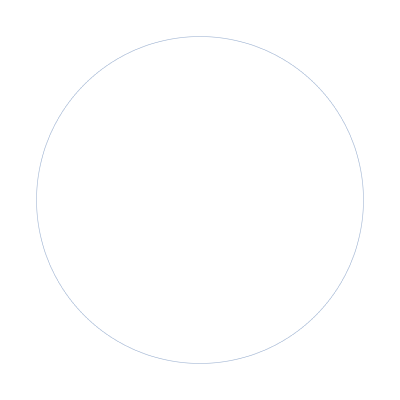

```mathematica
depth = 10; 
points = ({Re[#1], Im[#1]} & ) /@ Nest[invImage,
	{1},depth]; 
ListPlot[points, AspectRatio -> Automatic, 
	Axes -> False,
	PlotStyle -> {AbsolutePointSize[0.4]}]
```

The package function which encapsulates these commands is JuliaSimple.  Note that the second argument to JuliaSimple represents the depth rather than the total number of points.  Thus, the following command generates 2^12 points of an interesting Julia set.

```mathematica
Import["https://www.marksmath.org/JuliaSet.m"]
```

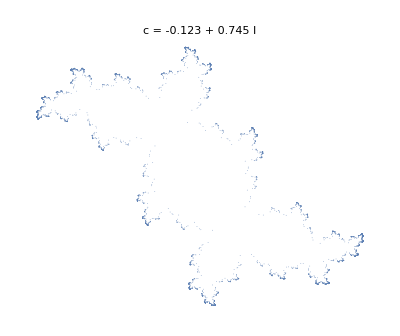

```mathematica
JuliaSimple[-0.123 + 0.745 I, 12, 
	PlotLabel -> "c = -0.123 + 0.745 I"]
```

## Improving The Simple Deterministic Algorithm

JuliaSimple is a short, fast, and easily understood algorithm.  However, our first interesting image above already indicates a weakness in the algorithm.  Some parts of the image seem more detailed than others.  This is because some parts of the Julia set are more attractive than others under the action of invImage.  In this section, we'll describe the function JuliaModified which fixes the problem.  Here is an example which compares the algorithms.

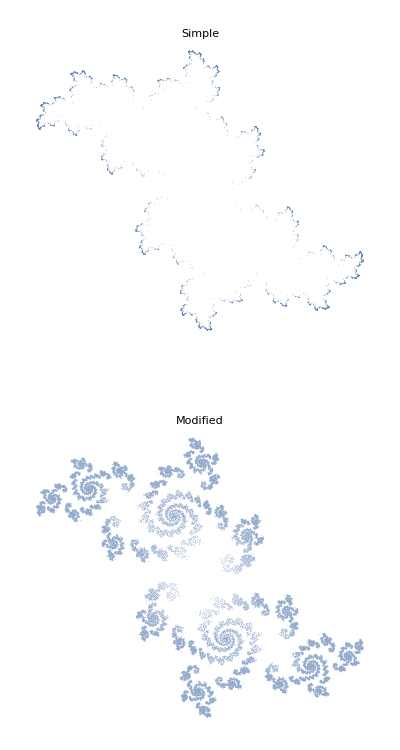

```mathematica
GraphicsGrid[{
	{JuliaSimple[0.68 I, 12, 
		DisplayFunction -> Identity, 
		PlotLabel -> "Simple"]},
	{JuliaModified[0.68 I,
		DisplayFunction -> Identity, 
		PlotLabel -> "Modified"]}}]
```

The simple algorithm clearly misses a great amount of detail.  A naive solution would be to increase the depth.  However, the required depth is frequently greater than 50, resulting in more than 2^50 points in the image.
     Here is a solution.  After a certain depth, we'll keep track of all of the points that have been plotted.  Points close together, as measured by the variable res, will be treated the same.  With each iteration, we'll apply invImage and discard points that have already been plotted.  As a result, the program will be able to run to a much larger depth since the length of the list of points no longer grows as 2^depth.  
     First, we need to rewrite invImage to treat points close together similarly.  We'll regenerate J_c for c=-0.123 + 0.745I.

```mathematica
c = -0.123 + 0.745 I; res = 200; 
invImage[points_] := Flatten[(Floor[{1, -1}
	res Sqrt[#1 - c]]/res & ) /@ 
	points];
```

The function reducedInvImage will accept a list of points, apply invImage, and return only those points that don't appear in the auxiliary variable, pointsSoFar.  As a side effect, it will update pointsSoFar.

```mathematica
reducedInvImage[points_] := Module[{newPoints},
	newPoints = Complement[invImage[points],
		pointsSoFar]; 
	pointsSoFar = Union[newPoints, pointsSoFar]; 
	newPoints];
```

Next, we'll iterate invImage several times from an arbitrary starting value to obtain some points close to J_c.  We'll store the result in pointsSoFar.

```mathematica
pointsSoFar = Nest[invImage, {1}, 5];
```

Now, we'll iterate reducedInvImage, starting with pointsSoFar, until it returns the empty list.

```mathematica
FixedPoint[reducedInvImage, pointsSoFar];
```

Finally, we ListPlot the points in pointsSoFar, after converting the complex numbers to ordered pairs.

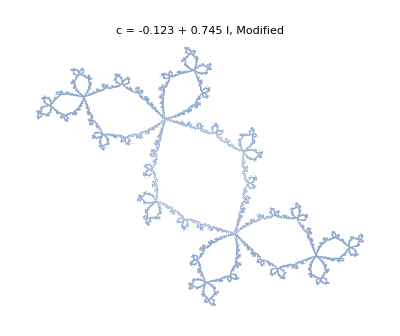

```mathematica
ListPlot[({Re[#1], Im[#1]} & ) /@ pointsSoFar, 
	AspectRatio -> Automatic, 
	Axes -> False, 
	PlotStyle -> {AbsolutePointSize[0.4]}, 
	PlotLabel -> "c = -0.123 + 0.745 I, Modified"]
```

Note that the level of detail is controlled by the option Resolution.  The default is Resolution→200.  We may get a  quick, less detailed image by using a smaller value for Resolution.  Here is an illustration of the effect of Resolution.

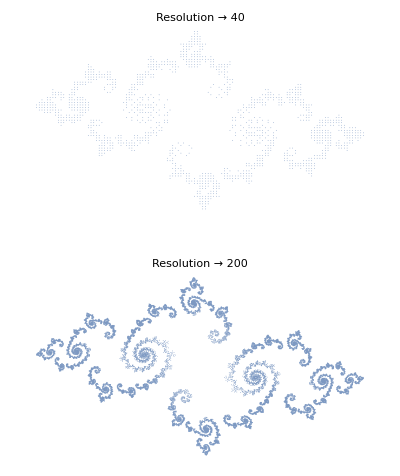

```mathematica
GraphicsGrid[{
	{JuliaModified[-0.77 + 0.22 I, 
		Resolution -> 40, 
		PlotLabel -> "Resolution → 40", 
		DisplayFunction -> Identity]}, 
    {JuliaModified[-0.77 + 0.22*I, 
		PlotLabel -> "Resolution → 200", 
		DisplayFunction -> Identity]}}]
```

### Comparing The Algorithms

The above images show much greater detail than was possible with JuliaSimple.  We can measure how large depth would have to be in JuliaSimple to achieve the same level of detail by replacing FixedPoint with FixedPointList and measuring its length.  Note that this computation will depend on the complexity of the Julia set.  We'll measure the depth for a fairly complicated Julia set.

```mathematica
c = 0.68 I; res = 200; 
invImage[points_] := Flatten[(Floor[{1, -1} 
	res Sqrt[#1 - c]]/res & ) /@ 
		points]; 
reducedInvImage[points_] := Module[{newPoints}, 
	newPoints = Complement[invImage[points], 
		pointsSoFar]; 
	pointsSoFar = Union[newPoints, pointsSoFar];
	newPoints]; 
pointsSoFar = Nest[invImage, {1}, 5]; 
Length[FixedPointList[reducedInvImage, pointsSoFar]]
```

77

Thus, JuliaSimple would need a depth of 77+5 to plot this particular Julia set resulting in a list of 2^82 points.  JuliaModified used barely 20,000 points to plot much more detail, as the following computation shows.

```mathematica
Length[pointsSoFar]
```

20408

## The Mandelbrot Set

Julia sets for quadratic functions of the form z^2+c are among the most important, because of their relationship with the Mandelbrot set.  The Mandelbrot set is defined to be the set of all c values that lead to connected Julia sets, J_c.  While it is not the purpose of this article to discuss the Mandelbrot set in detail, it is nice to have an image of it to assist in choosing interesting values of c.  The following code generates an image of the Mandelbrot set.  It is a minor modification of the code found in [Dickau 1997].  Points near the boundary frequently lead to interesting Julia sets.

```mathematica
MandelbrotFunction = Compile[{{c, _Complex}}, 
	Length[FixedPointList[#1^2 + c & , c, 100,
		SameTest -> (Abs[#2] > 2. & )]]]; 
DensityPlot[MandelbrotFunction[x + y*I], 
	{x, -2, 0.6}, {y, -1.3, 1.3}, 
	Mesh -> False, AspectRatio -> Automatic, 
	PlotPoints -> 300, 
	ColorFunction -> (If[#1 == 1, 
		RGBColor[0, 0, 0], Hue[0.9*#1]] & )]
```

-Graphics-

## Generalizing the Deterministic Algorithm

The algorithms described above apply only to functions of the specific form f_c(z)=z^2+c, but the theory is much more broadly applicable.  We should be able to apply the same ideas to any rational function whose inverses are known.  Let's apply these ideas to plot the Julia set of f(z) =z^3+z+.6I.

```mathematica
f[z_] = z^3 + z + 0.6*I; res = 200; 
inverses = z /. NSolve[f[z] == #1, z]; 
funcs = (Function[anInverse, N[Floor[anInverse*res]/res] & ]) /@ inverses;
```

A list of the inverses of f(z) is now held in funcs.  We need to turn this into invImage.

```mathematica
invImage[points_] := 
	Flatten[(Through[funcs[#1]] & ) /@ points, 1]; 
	invImage[{1}]
```

{-0.48-1.055 ⅈ,-0.26+1.285 ⅈ,0.73-0.24 ⅈ}

```mathematica
invImage[%]
```

{0.745-0.86 ⅈ,0.085+1.465 ⅈ,-0.835-0.615 ⅈ,0.07-1.255 ⅈ,0.4+0.775 ⅈ,-0.475+0.47 ⅈ,-0.515-0.95 ⅈ,-0.18+1.315 ⅈ,0.685-0.37 ⅈ}

Now the algorithm proceeds as before.

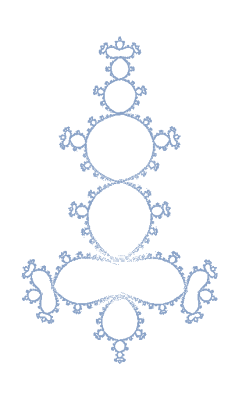

```mathematica
reducedImage[points_] := Module[{newPoints},
	newPoints = Complement[invImage[points], 
		pointsSoFar]; 
	pointsSoFar = 
		Union[newPoints, pointsSoFar]; newPoints];
pointsSoFar = Nest[invImage, {1.}, 5]; 
FixedPoint[reducedImage, pointsSoFar]; 
ListPlot[({Re[#1], Im[#1]} & ) /@ pointsSoFar, 
	AspectRatio -> Automatic, 
	Axes -> False, 
	PlotStyle -> {AbsolutePointSize[0.4]}]
```

These commands are encapsulated in the package function Julia.  Here are two more examples.

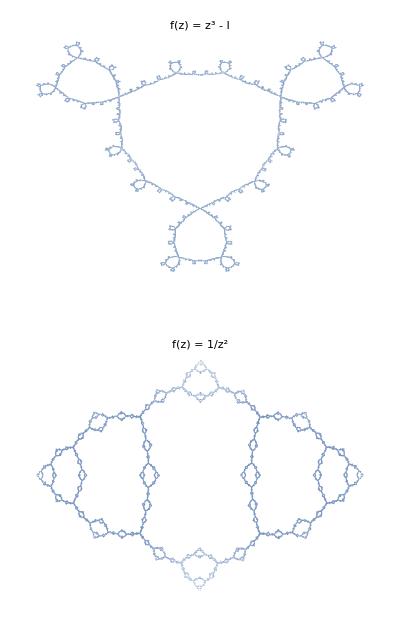

```mathematica
GraphicsGrid[
	{{Julia[z^3-I,z,
		PlotLabel -> "f(z) = z^3 - I",
		DisplayFunction -> Identity]},
	{Julia[1/(z^2-1),z,
		PlotLabel -> "f(z) = 1/z^2"]}}]
```

Note that the second image in the preceeding example is the Julia set of a rational function. We, actually, need to make one final adjustment to generate Julia sets of  rational functions.  Our method for pruning points depends upon the fact that the Julia set is bounded.  While this assumption is valid for polynomials, the Julia set of a rational function need not be bounded.  In this case, the function reducedImage should throw out points that are larger than some specified bound, in addition to points that have already been plotted.  Here is the modified version of reducedImage.

```mathematica
bound = 4; 
reducedImage[points_] := Module[{newPoints},
	newPoints = 
		Complement[image[points], pointsSoFar];
	newPoints = 
		Select[newPoints, N[Abs[#1]] <= bound & ]; 
	pointsSoFar = 
		Union[newPoints, pointsSoFar];
	newPoints]
```

The package function Julia uses this version of reducedImage when called with a rational function.  The value of bound is controlled by the option Bound.  The default is Bound→4.  We illustrate the use of Bound by plotting the Julia set of the rational function used to find the roots of z^3=1 with Newton's method.

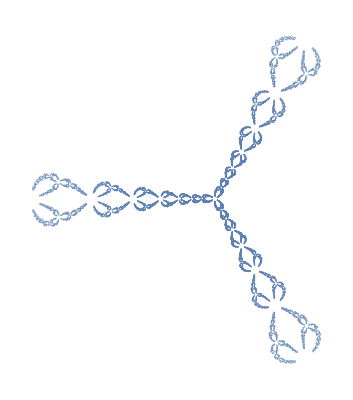

```mathematica
Julia[(2z)/3+1/(3 z^2),z,Bound -> 12]
```

## A Stochastic Algorithm

This article would not be complete without a discussion of the random inverse iteration algorithm.  This is probably the simplest, and fastest, way to generate the Julia set of a quadratic function.  The random inverse iteration algorithm, also, highlights the similarities between Julia sets and self-similar sets, because of its resemblance to the chaos game [Devaney 1992, sec. 14.1].  

Suppose we would like to generate 1000 points of the Julia set for c=0.

```mathematica
c = 0.; numPoints = 1000;
```

As we've seen, J_c is attractive under the action of both inverses of f_c.

```mathematica
inv1 = Sqrt[#1 - c] & ; inv2 = -Sqrt[#1 - c] & ;
```

We choose the number 1 as an arbitrary starting point.  We then choose one of the inverses inv1 or inv2 randomly and apply it to the starting point 1.  Continuing, we iterate this procedure, choosing a random inverse and applying it to the previous point.  This generates a list of points converging to J_c.  We drop the first few points, since they might not be close to J_c, and plot the rest.  We implement this idea in Mathematica by using Table to generate a list of length numPoints, where each entry is either inv1 or inv2 with equal probability.  We then use ComposeList to build the list of points.

```mathematica
points = Drop[ComposeList[Table[chooser = Random[]; 
	If[chooser < 0.5, inv1, 
		inv2], {numPoints}], 1], 10];
```

Finally, we plot these points, after converting them to ordered pairs.

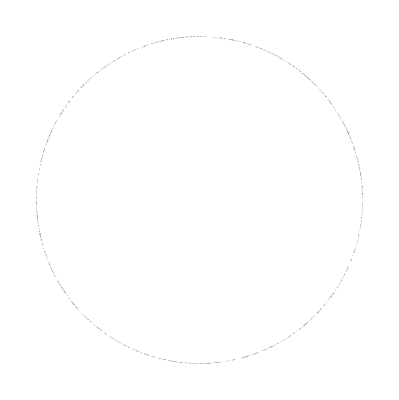

```mathematica
ListPlot[({Re[#1], Im[#1]} & ) /@ points, 
	AspectRatio -> Automatic, 
	Axes -> False, 
	PlotStyle -> {AbsolutePointSize[0.4]}]
```

These commands are encapsulated in the package function JuliaStochastic.  Unfortunately, images generated in this manner frequently display the same nonuniform distribution we saw with JuliaSimple.  The random inverse iteration algorithm may be improved, for some Julia sets, by skewing the probability of choosing one inverse over the other.  This accomplished in our function JuliaStochastic with the option OneBias, which is a real number, strictly between 0 and 1, indicating the probability of choosing inv1.  The probability of choosing inv2 is then, necessarily, 1-OneBias.  The following example illustrates the effect of OneBias.

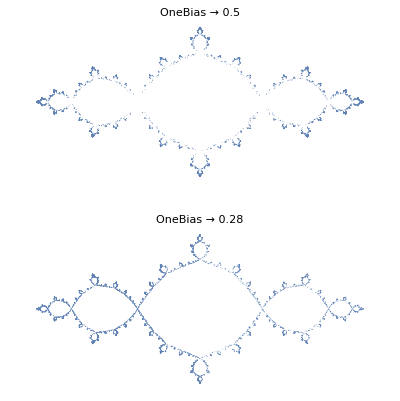

```mathematica
GraphicsGrid[{
	{JuliaStochastic[-1, 8000, 
		PlotLabel -> "OneBias → 0.5", 
		DisplayFunction -> Identity]}, 
    {JuliaStochastic[-1, 8000, 
		OneBias -> 0.28, 
		PlotLabel -> "OneBias → 0.28", 
		DisplayFunction -> Identity]}}]
```

In general, the inverse which is more contractive about its fixed point should be assigned a lower probability.  The contractivity of a function about its fixed point is measured by the value of its derivative.  Thus for c=-1, as above we have the following.

```mathematica
c = -1.; 
inv1 = Sqrt[#1 - c] & ; 
inv2 = -Sqrt[#1 - c] & ; 
{inv1FixedPoint, inv2FixedPoint} = Chop[{FixedPoint[inv1, 1, 1000], FixedPoint[inv2, 1, 1000]}]
```

{1.61803,-0.618034}

With the fixed points, we may now measure the contractivity.

```mathematica
{Abs[D[inv1[x], x]] /. 
	x -> inv1FixedPoint, 
Abs[D[inv2[x], x]] /. 
	x -> inv2FixedPoint}
```

{0.309017,0.809017}

This suggests we should choose OneBias to be less than .5, since inv1 is more contractive than inv2.  Unfortunately, many Julia sets have much more detail than the random inverse algorithm will generate for any choice of OneBias.  For example, suppose c=0.68 I.

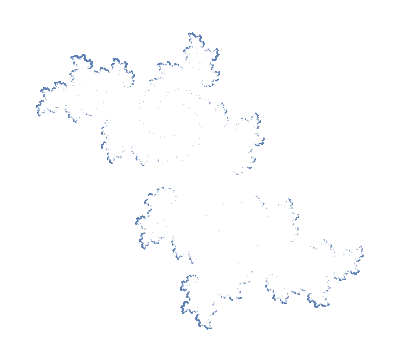

```mathematica
JuliaStochastic[0.68 I, 40000, OneBias -> 0.23]
```

Experimentation suggests that a value of 0.23 is close to optimal for OneBias.  However, the modified inverse iterated algorithm shows much more detail using far fewer points.  Therefore, we will not pursue the random algorithm further.

## References

Beardon, A.F.  1991.  Iteration of Rational Functions.  Springer-Verlag New York Graduates Texts in Mathematics 132.

Carleson, L. and Gamelin, T.W.  1993.  Complex Dynamics.  Springer-Verlag New York.

Devaney, R.L. 1992. A First Course in Chaotic Dynamical Systems. Addison-Wesley Reading, Mass.

Dickau, R.M.  1997. Compilation of iterative and list operations in "Tricks of the Trade." The Mathematica Journal.  7(1): 14-15.

Fatou, M.P.  1919.  Sur les equations fonctionelles.  Bull. Soc. Math. France.  47:161-271.

Julia, G.  1918.  Memoire sur l'iteration des fonctions rationelles.  Math. Pures Appl., 8:47-245.

Peitgen, H.O. and Richter, P.  1989.  The Beauty of Fractals.  Springer-Verlag Heidelberg.

## About the Author

Mark McClure is an assistant professor of mathematics at the University of North Carolina at Asheville.  He received his Ph.D. in mathematics from the Ohio State University under the direction of Gerald Edgar.  His primary research interest is the study of fractal dimensions of various sets arising in real analysis.  He was introduced to Mathematica through the Calculus&Mathematica program at OSU.

Mark McClure
Department of Mathematics
University of North Carolina at Asheville
Asheville, North Carolina 28804
mcmcclur@bulldog.unca.edu
http://www.unca.edu/~mcmcclur/

## Addenda

### JuliaSetPlot

As of Mathematica V10, the fabulous new function JuliaSetPlot implements inverse iteration, as well as the classic escape time algorithm. To force Mathematica to use inverse iteration, simply use the option ColorFunction→ None.

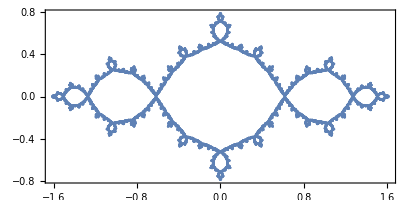

```mathematica
JuliaSetPlot[-1, ColorFunction->None]
```

### Why are some parts of the Julia set more attractive than other parts

The fact that some parts of the Julia set are more attractive than other parts is a simple consequence of the fact that the derivative is not constant over the Julia set. To illustrate this, let’s examine a Julia set together with its two fixed points.

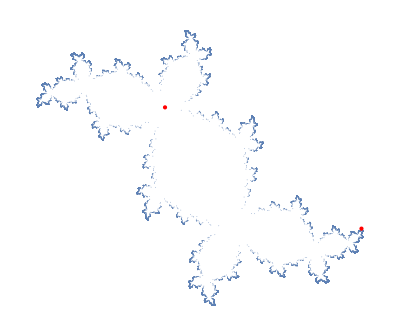

```mathematica
c = -0.123+0.745I;
f[z_] = z^2+c;
fixedPoints = z/.NSolve[f[z]==z,z];
JuliaSimple[c,15,Epilog -> {Red,PointSize[Large],
Point[{Re[#],Im[#]}& /@ fixedPoints]
}]
```

Both of those fixed points are repelling, as they lie in the Julia set. One is in a hard to reach spot in the Julia set while the other is in a much more frequently traveled spot. The degree to which they repel can be measured by the absolute value of the derivative.

```mathematica
Abs[f'/@fixedPoints]
```

{1.10739,2.72745}

Note that one repels much more weakly than the other. Furthermore, the reciprocals of these numbers indicate how attractive the points are under inverse iteration.

```mathematica
1/%
```

{0.903026,0.366643}

Thus, that first point (where the derivative is close to one) should be much harder to get to under inverse iteration.